Constant Mdot Solver


Function definitions

```mathematica
αdisk[x_,rout_]:=λi + (λo-λi) (x/nu[x] - ri/nu[ri])/(rout/nu[rout]-ri/nu[ri]) 
αdisk2[x_,lamin_,lamout_,rin_,rout_]:=lamin+ (lamout-lamin) (x/nu[x] - rin/nu[rin])/(rout/nu[rout]-rin/nu[rin])
nu[x_]:= α h^2 x^γ
vrn[x_,rout_]:= -1.5 (λo-λi)/(rout/nu[rout]-ri/nu[ri]) /αdisk[x,rout]
ξ[x_]:= (x-a)/q
Func[x_]:= T0 *((Γ+1)Exp[-((ξ[x]-β)/Δ)^2] -Exp[-((ξ[x]+β)/Δ)^2])/(Δ Sqrt[Pi])
s[x_,x0_,w_]:= .5(1 + Tanh[(x-x0)/w])
Λinteg[x_]:= x+(a^2 (13 a^2-30 a x+18 x^2))/(3 (a-x)^3)+4 a Log[-a+x]
ΛnormR[c_]:= Λinteg[ro]-Λinteg[a+c rh]
ΛnormL[c_]:= Λinteg[a-c rh]-Λinteg[ri]
ΛL[x_,f_,c_]:= -f Pi (μ h^3)^2 (x/(x-a))^4 / ΛnormL[c]
ΛR[x_,f_,c_]:= f Pi (μ h^3)^2 (x/(x-a))^4  / ΛnormR[c]
Piecewise[{{- f Pi (μ h^3)^2 (x/(x-a))^4,x<(a-c rh)},{0,a-c rh ≤ x≤ a+c rh},{f Pi (μ h^3)^2 (x/(x-a))^4,x>(a+c rh)}}]
Λsmooth[x_,f_,c_,w_]:=(1-s[x,a-c rh,w])ΛL[x,f,c]+ s[x,a-c rh,w] s[x,a + c rh,w] ΛR[x,f,c]
```

Piecewise[{{-(f h^6 π x^4 μ^2)/(-a+x)^4, x<a-c rh}, {0, a-c rh≤x≤a+c rh}, {(f h^6 π x^4 μ^2)/(-a+x)^4, x>a+c rh}, {0, True}}]

## Default Global Variables

```mathematica
PlanetFlag = 1
a=10;
γ=.5;
μ=1;
h=.1;
α=.06;
β=2/3;
Δ = 1;
Γ = 0;
ri = 1;
ro = 100;
λi = 10^(-3);
λo = 1;
Λf = 1;
Λc = 2/3; 
Λw=.01;
rh = (μ h^3/3)^(1./3) a;
q= Max[h,rh];
T0 = 2 Pi a μ^2 h^3/h;
```

1

## Simple Example

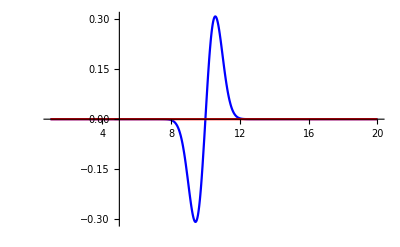

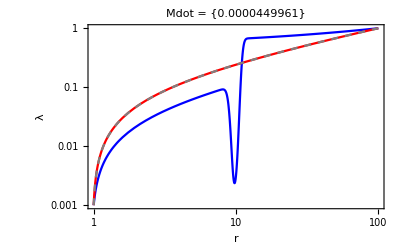

{InterpolatingFunction[{{1., 100.}}, <>][r]}

{InterpolatingFunction[{{1., 100.}}, <>][r]}

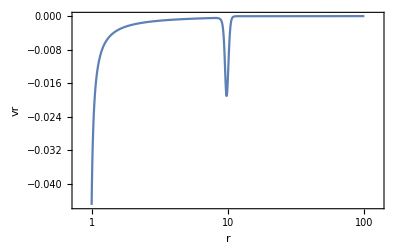

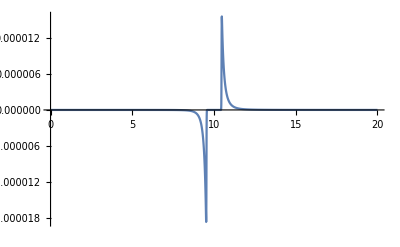

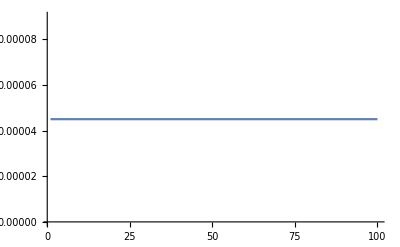

{-0.0000999001}

```mathematica
Plot[{Func[r],Λsmooth[r,Λf,Λc,Λw]},{r,ri,a+10},PlotRange->Full,PlotStyle->{Blue,Red}]
sol=NDSolve[ {3 nu[r] λ'[r] + λ[r](3 nu[r](γ-.5)/r - PlanetFlag  Func[r] /(Pi  Sqrt[r])) == m[r],m'[r]== 0,λ[ri]== λi,λ[ro]== λo},{λ,m},{r,ri,ro}];
sol1=NDSolve[ {3 nu[r] λ'[r] + λ[r](3 nu[r](γ-.5)/r - PlanetFlag  Λsmooth[r,Λf,Λc,Λw] /(Pi  Sqrt[r])) == m[r],m'[r]== 0,λ[ri]== λi,λ[ro]== λo},{λ,m},{r,ri,ro}];
LogLogPlot[{λ[r]/.sol,λ[r]/.sol1,αdisk[r,ro]},{r,ri,ro},PlotRange-> {{ri,ro},{.001,1}},Frame-> True,Axes->False,FrameLabel->{"r","λ"},PlotLabel->  Row@{"Mdot = ", Evaluate[m[ri]/.sol]},PlotStyle->{Blue,Red,{Dashed,Gray}}]
LogLinearPlot[Evaluate[-m[r]/λ[r]/.sol],{r,ri,ro},PlotRange-> Full,Frame-> True,Axes->False,FrameLabel->{"r","vr"},PlotLabel->Print[Evaluate[m[r]/.sol1]]]
Plot[Λsmooth[r,Λf,Λc,Λw],{r,0,a+10},PlotRange->Full]
Plot[m[r]/.sol,{r,ri,ro}]
Print[ -m[3] /.sol1]
```

```mathematica
Different Outer λ
```

{RGBColor[0.24720000000000014, 0.24, 0.6],RGBColor[0.6, 0.24, 0.4428931686004542],RGBColor[0.6, 0.5470136627990908, 0.24],RGBColor[0.24, 0.6, 0.33692049419863584],RGBColor[0.24, 0.3531726744018182, 0.6],RGBColor[0.6, 0.24, 0.5632658430022722],RGBColor[0.6, 0.42664098839727194, 0.24]}

0.001

Power::infy: Infinite expression 1/0. encountered.

0.003

0.01

0.03

0.1

0.3

1

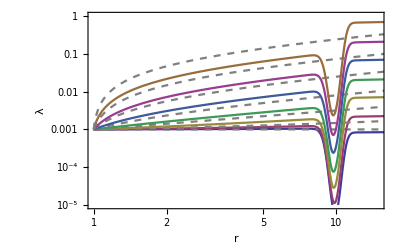

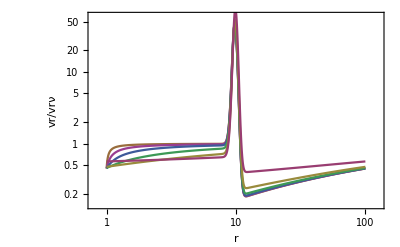

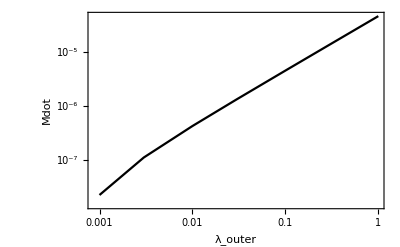

```mathematica
lamlist={.001,.003,.01,.03,.1,.3,1};
clist = Table[ColorData[1][i],{i,1,Length[lamlist]}]
lams={};
plts= {};
plts1={};
vrs={};
mdots={};
For[i=1,i≤ Length[lamlist],i++,λo=lamlist[[i]];Print[λo]; sol=NDSolve[ {3 nu[r] λ'[r] + λ[r](3 nu[r](γ-.5)/r - PlanetFlag Func[r]/(Pi Sqrt[r]))== m[r],m'[r]== 0,λ[ri]== λi,λ[ro]== λo},{λ,m},{r,ri,ro}];
AppendTo[mdots,Evaluate[m[ri]/.sol][[1]]];
AppendTo[lams,Evaluate[λ[r]/.sol][[1]]];
AppendTo[vrs,Evaluate[ -m[r]/λ[r] /.sol][[1]]];
AppendTo[plts,LogLogPlot[{Evaluate[λ[r]/.sol],αdisk[r,ro]},{r,ri,ro},Frame->True,Axes->False,PlotRange->{{1,15},{10^(-5),1}},FrameLabel->{"r","λ"},PlotStyle->{clist[[i]],{Dashed,Gray}}]];
AppendTo[plts1,LogLogPlot[ Evaluate[ -m[ri]/λ[r]/vrn[r,ro] /.sol],{r,ri,ro},PlotRange->Full,Frame->True,Axes->False,FrameLabel->{"r","vr/vrν"},PlotStyle->{clist[[i]]}]];]
Show[plts]
Show[Reverse[plts1]]
ListLogLogPlot[Thread[{lamlist,mdots}],Joined->True,Frame->True,Axes->False,FrameLabel->{"λ_outer","Mdot"},PlotStyle->Black]
```

```mathematica
Different α values
```

{RGBColor[0., 0., 0.],RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862],RGBColor[0.996078431372549, 0.9882352941176471, 0.03529411764705882],RGBColor[0.5411764705882353, 0.7137254901960784, 0.027450980392156862],RGBColor[0.1450980392156863, 0.43529411764705883, 0.3843137254901961]}

0.06

0.1

0.3

0.6

1

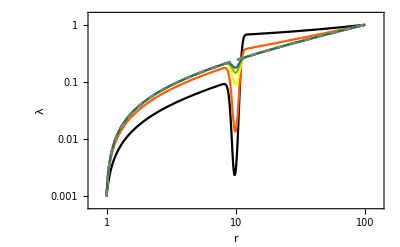

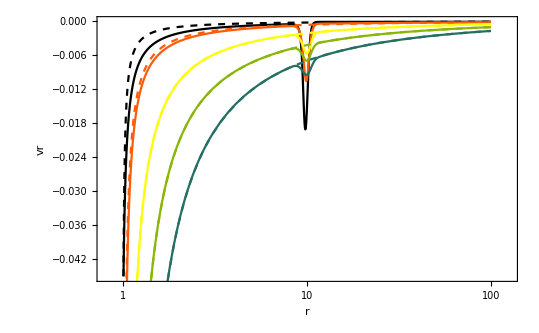

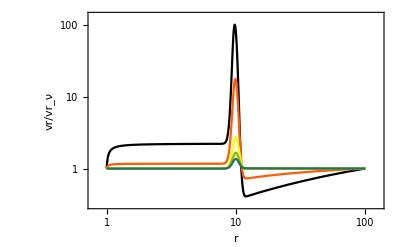

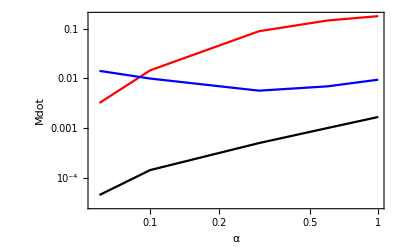

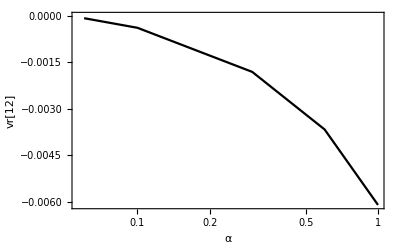

```mathematica
λo = 1; ro=100; ri=1; λi=10^(-3); μ=1; h =.1;
alist={.06,.1,.3,.6,1};
clist = Table[ColorData[3][i],{i,1,Length[alist]}]
lams={};
plts= {};
plts1={};
plts2={};
mdots={};
vrs={};
For[i=1,i≤ Length[alist],i++,α=alist[[i]];Print[α]; sol=NDSolve[ {3 nu[r] λ'[r] + λ[r](3 nu[r](γ-.5)/r - PlanetFlag Func[r]/(Pi Sqrt[r]))== m[r],m'[r]== 0,λ[ri]== λi,λ[ro]== λo},{λ,m},{r,ri,ro}];
AppendTo[mdots,Evaluate[m[ri]/.sol][[1]]];
AppendTo[vrs,Evaluate[m[r]/(-λ[r])/.sol][[1]]];
AppendTo[lams,Evaluate[λ[r]/.sol][[1]]];
AppendTo[plts,LogLogPlot[{Evaluate[λ[r]/.sol],αdisk[r,ro]},{r,ri,ro},Frame->True,Axes->False,(*PlotRange->{{1,15},{10^(-5),1}},*)FrameLabel->{"r","λ"},PlotStyle->{clist[[i]],{Dashed,Gray}}]];
AppendTo[plts1,LogLinearPlot[{vrs[[i]],-mdots[[i]]/αdisk[r,ro]},{r,ri,ro},Frame->True,Axes->False,(*PlotRange->{{1,15},{10^(-5),1}},*)PlotRange->Full,FrameLabel->{"r","vr"},PlotStyle->{clist[[i]],{Dashed,clist[[i]]}}]];
AppendTo[plts2,LogLogPlot[vrs[[i]]/(-mdots[[i]]/αdisk[r,ro]),{r,ri,ro},Frame->True,Axes->False,(*PlotRange->{{1,15},{10^(-5),1}},*)PlotRange->Full,FrameLabel->{"r","vr/vr_ν"},PlotStyle->{clist[[i]]}]];]
Show[plts]
Show[plts1]
Show[plts2]
ListLogLogPlot[{Thread[{alist,mdots}],Thread[{alist,Table[lams[[i]] /.r-> a,{i,1,Length[lams]}](*Table[FindMinValue[{lams[[i]]/.r-> x,ri≤ x≤ ro},x],{i,1,Length[alist]}]*)}],Thread[{alist,Table[Abs[vrs[[i]]/.r->a],{i,1,Length[vrs]}]}]},Joined->True,Frame->True,Axes->False,FrameLabel->{"α","Mdot"},PlotStyle->{Black,Red,Blue}]
ListLogLinearPlot[Thread[{alist,Table[vrs[[i]]/.r-> 12,{i,1,Length[alist]}]}],Joined->True,Frame->True,Axes->False,FrameLabel->{"α","vr[12]"},PlotStyle->Black]
```

## Different Outer radius

0

{RGBColor[0.24720000000000014, 0.24, 0.6],RGBColor[0.6, 0.24, 0.4428931686004542],RGBColor[0.6, 0.5470136627990908, 0.24],RGBColor[0.24, 0.6, 0.33692049419863584],RGBColor[0.24, 0.3531726744018182, 0.6]}

100

50

30

20

15

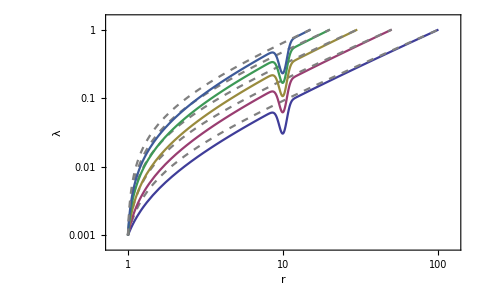

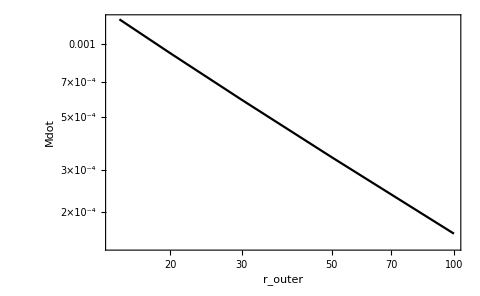

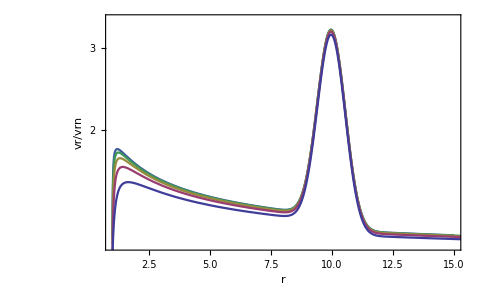

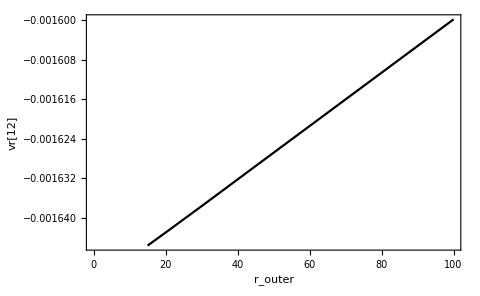

```mathematica
rolist=Reverse[{15,20,30,50,100}];
λo = 1; λi =10^(-3); ri=1; Γ=0; μ = 8; γ=0
clist = Table[ColorData[1][i],{i,1,Length[rolist]}]
lams={};
plts= {};
plts1={};
mdots={};
vrs={};
For[i=1,i≤ Length[rolist],i++,ro=rolist[[i]];Print[ro]; sol=NDSolve[ {3 nu[r] λ'[r] + λ[r](3 nu[r](γ-.5)/r - PlanetFlag Func[r]/(Pi Sqrt[r]))== m[r],m'[r]== 0,λ[ri]== λi,λ[ro]== λo},{λ,m},{r,ri,ro}];
AppendTo[mdots,Evaluate[m[ri]/.sol][[1]]];
AppendTo[vrs,Evaluate[m[r]/(-λ[r])/.sol][[1]]];
AppendTo[lams,Evaluate[λ[r]/.sol]];
AppendTo[plts,LogLogPlot[{Evaluate[λ[r]/.sol],αdisk[r,ro]},{r,ri,ro},Frame->True,Axes->False,(*PlotRange->{{1,15},{10^(-5),1}},*)FrameLabel->{"r","λ"},PlotStyle->{clist[[i]],{Dashed,Gray}}]];
AppendTo[plts1,LogPlot[vrs[[i]]/vrn[r,ro],{r,ri,ro},Frame->True,Axes->False,PlotRange->Full,FrameLabel->{"r","vr/vrn"},PlotStyle->{clist[[i]]}]];]
Show[plts]
ListLogLogPlot[Thread[{rolist,mdots}],Joined->True,Frame->True,Axes->False,FrameLabel->{"r_outer","Mdot"},PlotStyle->Black]
Show[Reverse[plts1]]
ListPlot[Thread[{rolist,Table[vrs[[i]]/.r-> 12,{i,1,Length[rolist]}]}],Joined->True,Frame->True,Axes->False,FrameLabel->{"r_outer","vr[12]"},PlotStyle->Black]
```

### Different Outer Radius, Same initial profile

{RGBColor[0.24720000000000014, 0.24, 0.6],RGBColor[0.6, 0.24, 0.4428931686004542],RGBColor[0.6, 0.5470136627990908, 0.24],RGBColor[0.24, 0.6, 0.33692049419863584],RGBColor[0.24, 0.3531726744018182, 0.6]}

100

50

30

20

15

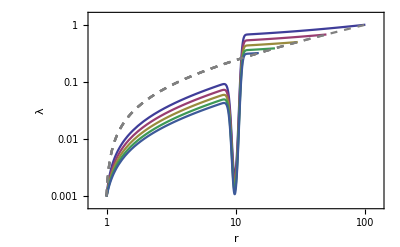

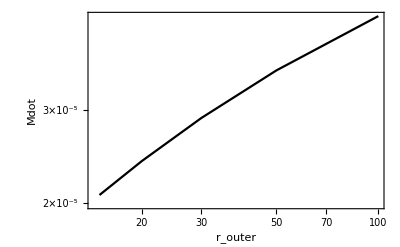

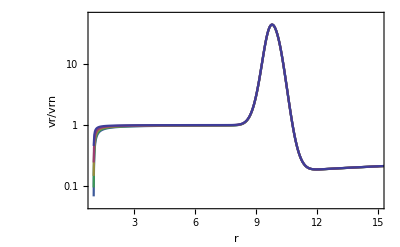

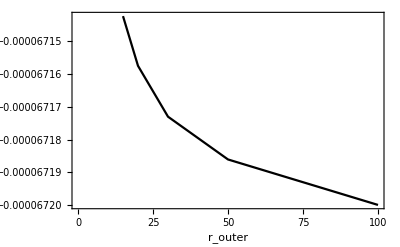

```mathematica
rolist=Reverse[{15,20,30,50,100}];
λo = 1; λi =10^(-3); ri=1; Γ=0;
clist = Table[ColorData[1][i],{i,1,Length[rolist]}]
lams={};
plts= {};
plts1={};
mdots={};
vrs={};
For[i=1,i≤ Length[rolist],i++,ro=rolist[[i]];Print[ro]; sol=NDSolve[ {3 nu[r] λ'[r] + λ[r](3 nu[r](γ-.5)/r - PlanetFlag Func[r]/(Pi Sqrt[r]))== m[r],m'[r]== 0,λ[ri]== λi,λ[ro]== αdisk2[ro,λi,λo,ri,rolist[[1]]]},{λ,m},{r,ri,ro}];
AppendTo[mdots,Evaluate[m[ri]/.sol][[1]]];
AppendTo[vrs,Evaluate[m[r]/(-λ[r])/.sol][[1]]];
AppendTo[lams,Evaluate[λ[r]/.sol]];
AppendTo[plts,LogLogPlot[{Evaluate[λ[r]/.sol],αdisk2[r,λi,λo,ri,rolist[[1]]]},{r,ri,ro},Frame->True,Axes->False,(*PlotRange->{{1,15},{10^(-5),1}},*)FrameLabel->{"r","λ"},PlotStyle->{clist[[i]],{Dashed,Gray}}]];
AppendTo[plts1,LogPlot[vrs[[i]]/vrn[r,ro],{r,ri,ro},Frame->True,Axes->False,PlotRange->Full,FrameLabel->{"r","vr/vrn"},PlotStyle->{clist[[i]]}]];]
Show[plts]
ListLogLogPlot[Thread[{rolist,mdots}],Joined->True,Frame->True,Axes->False,FrameLabel->{"r_outer","Mdot"},PlotStyle->Black]
Show[Reverse[plts1]]
ListPlot[Thread[{rolist,Table[vrs[[i]]/.r-> 12,{i,1,Length[rolist]}]}],Joined->True,Frame->True,Axes->False,FrameLabel->{"r_outer","vr[12]"},PlotStyle->Black]
```

## Different Inner Radius

{RGBColor[0.24720000000000014, 0.24, 0.6],RGBColor[0.6, 0.24, 0.4428931686004542],RGBColor[0.6, 0.5470136627990908, 0.24],RGBColor[0.24, 0.6, 0.33692049419863584]}

0.01

0.1

1

3

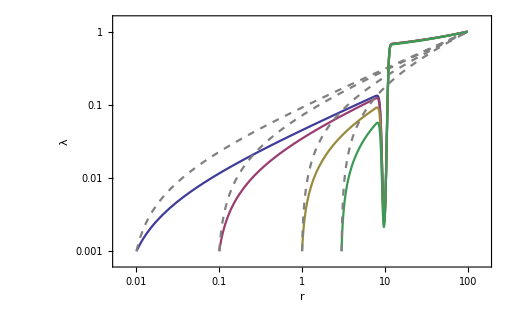

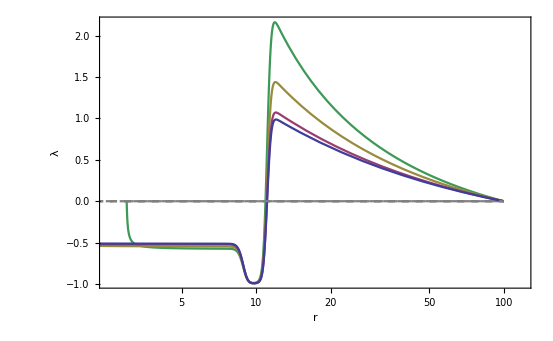

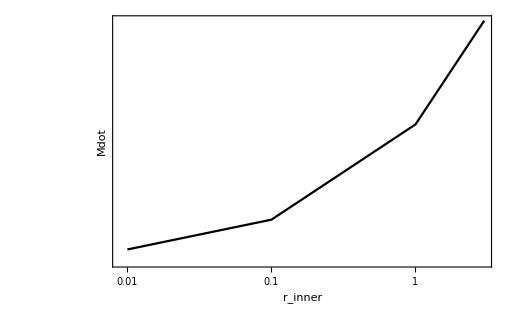

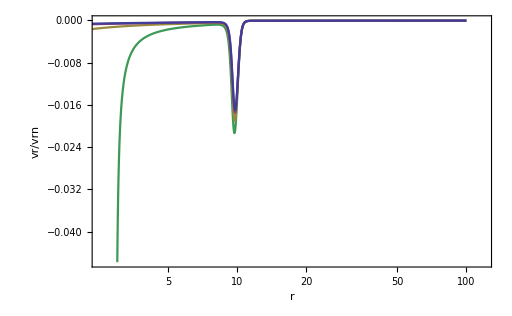

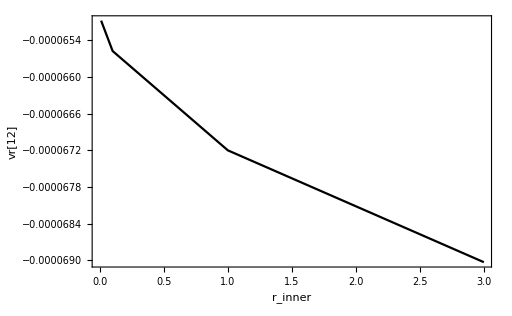

```mathematica
rilist={.01,.1,1,3};
λo = 1; λi =10^(-3); ro=100; Γ=0; α = .06; h=.1;
clist = Table[ColorData[1][i],{i,1,Length[rilist]}]
lams={};
plts= {};
plts1={};
plts2={};
mdots={};
vrs={};
For[i=1,i≤ Length[rilist],i++,ri=rilist[[i]];Print[ri]; sol=NDSolve[ {3 nu[r] λ'[r] + λ[r](3 nu[r](γ-.5)/r - PlanetFlag Func[r]/(Pi Sqrt[r]))== m[r],m'[r]== 0,λ[ri]== λi,λ[ro]== λo},{λ,m},{r,ri,ro}];
AppendTo[mdots,Evaluate[m[ri]/.sol][[1]]];
AppendTo[vrs,Evaluate[m[r]/(-λ[r])/.sol][[1]]];
AppendTo[lams,Evaluate[λ[r]/.sol]];
AppendTo[plts,LogLogPlot[{Evaluate[λ[r]/.sol],αdisk[r,ro]},{r,ri,ro},Frame->True,Axes->False,FrameLabel->{"r","λ"},PlotStyle->{clist[[i]],{Dashed,Gray}}]];
AppendTo[plts2,LogLinearPlot[{Evaluate[(λ[r]-αdisk[r,ro])/αdisk[r,ro]/.sol],0},{r,ri,ro},PlotRange->Full,Frame->True,Axes->False,FrameLabel->{"r","Δλ/λ"},PlotStyle->{clist[[i]],{Dashed,Gray}}]];
AppendTo[plts1,LogLinearPlot[vrs[[i]],{r,ri,ro},Frame->True,Axes->False,PlotRange->Full,FrameLabel->{"r","vr/vrn"},PlotStyle->{clist[[i]]}]];]
Show[plts]
Show[Reverse[plts2]]
ListLogLogPlot[Thread[{rilist,mdots}],Joined->True,Frame->True,Axes->False,FrameLabel->{"r_inner","Mdot"},PlotStyle->Black]
Show[Reverse[plts1]]
ListPlot[Thread[{rilist,Table[vrs[[i]]/.r-> 12,{i,1,Length[rilist]}]}],Joined->True,Frame->True,Axes->False,FrameLabel->{"r_inner","vr[12]"},PlotStyle->Black]
```

## Different Inner Radius on Same initial profile

{RGBColor[0.24720000000000014, 0.24, 0.6],RGBColor[0.6, 0.24, 0.4428931686004542],RGBColor[0.6, 0.5470136627990908, 0.24],RGBColor[0.24, 0.6, 0.33692049419863584]}

0.01

0.1

1

3

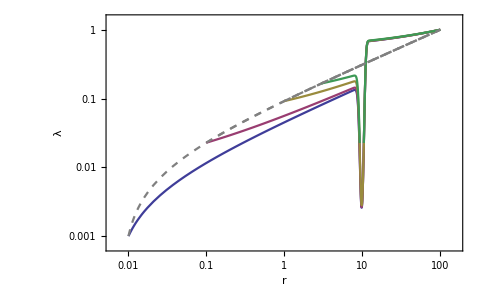

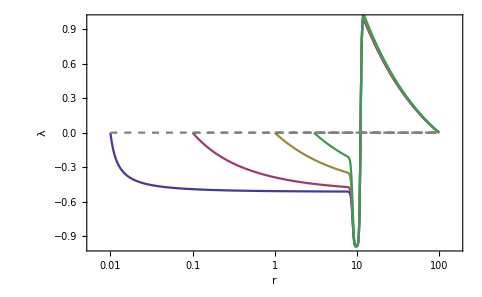

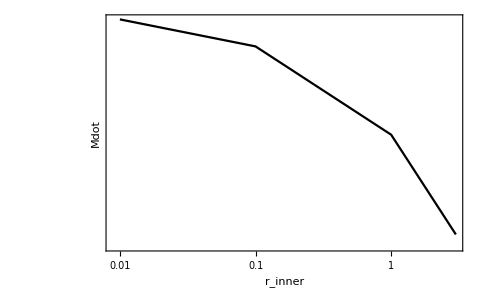

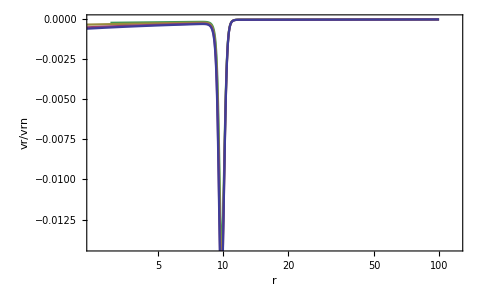

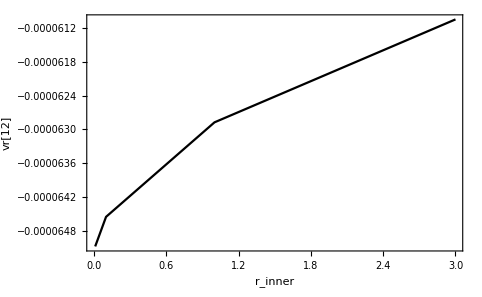

```mathematica
rilist={.01,.1,1,3};
λo = 1; λi =10^(-3); ro=100; Γ=0; α = .06; h=.1; 
clist = Table[ColorData[1][i],{i,1,Length[rilist]}]
lams={};
plts= {};
plts1={};
plts2={};
mdots={};
vrs={};
For[i=1,i≤ Length[rilist],i++,ri=rilist[[i]];Print[ri]; sol=NDSolve[ {3 nu[r] λ'[r] + λ[r](3 nu[r](γ-.5)/r - PlanetFlag Func[r]/(Pi Sqrt[r]))== m[r],m'[r]== 0,λ[ri]== αdisk2[ri,λi,λo,rilist[[1]],ro],λ[ro]== λo},{λ,m},{r,ri,ro}];
AppendTo[mdots,Evaluate[m[ri]/.sol][[1]]];
AppendTo[vrs,Evaluate[m[r]/(-λ[r])/.sol][[1]]];
AppendTo[lams,Evaluate[λ[r]/.sol]];
AppendTo[plts,LogLogPlot[{Evaluate[λ[r]/.sol],αdisk2[r,λi,λo,rilist[[1]],ro]},{r,ri,ro},Frame->True,Axes->False,FrameLabel->{"r","λ"},PlotStyle->{clist[[i]],{Dashed,Gray}}]];
AppendTo[plts2,LogLinearPlot[{Evaluate[(λ[r]-αdisk2[r,λi,λo,rilist[[1]],ro])/αdisk2[r,λi,λo,rilist[[1]],ro]/.sol],0},{r,ri,ro},PlotRange->Full,Frame->True,Axes->False,FrameLabel->{"r","λ"},PlotStyle->{clist[[i]],{Dashed,Gray}}]];
AppendTo[plts1,LogLinearPlot[vrs[[i]],{r,ri,ro},Frame->True,Axes->False,PlotRange->Full,FrameLabel->{"r","vr/vrn"},PlotStyle->{clist[[i]]}]];]
Show[plts]
Show[plts2]
ListLogLogPlot[Thread[{rilist,mdots}],Joined->True,Frame->True,Axes->False,FrameLabel->{"r_inner","Mdot"},PlotStyle->Black]
Show[Reverse[plts1]]
ListPlot[Thread[{rilist,Table[vrs[[i]]/.r-> 12,{i,1,Length[rilist]}]}],Joined->True,Frame->True,Axes->False,FrameLabel->{"r_inner","vr[12]"},PlotStyle->Black]
```

## Different Mach Numbers

{RGBColor[0.24720000000000014, 0.24, 0.6],RGBColor[0.6, 0.24, 0.4428931686004542],RGBColor[0.6, 0.5470136627990908, 0.24],RGBColor[0.24, 0.6, 0.33692049419863584],RGBColor[0.24, 0.3531726744018182, 0.6]}

0.05

0.07

0.1

0.2

0.3

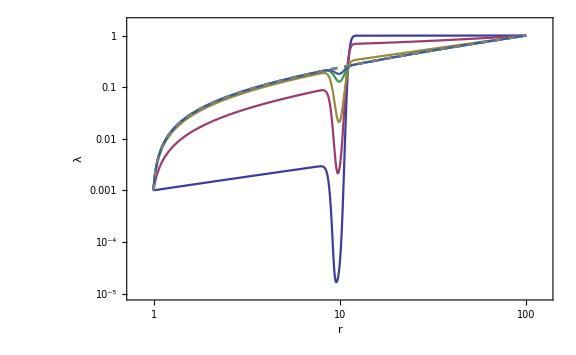

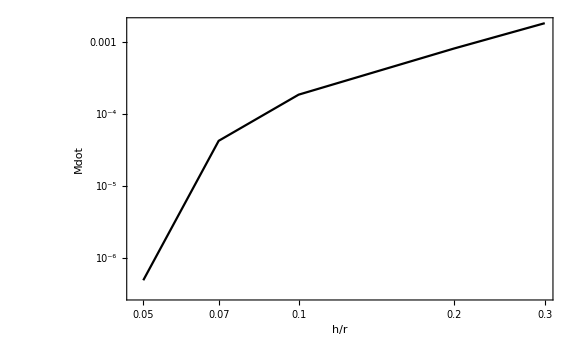

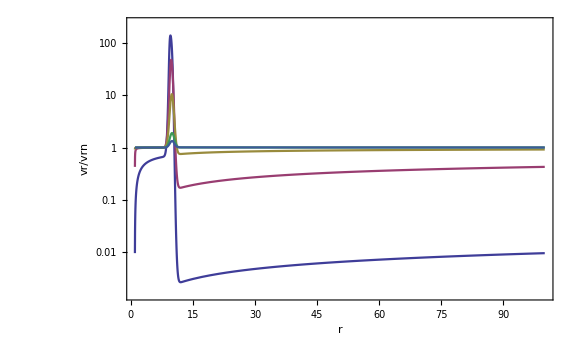

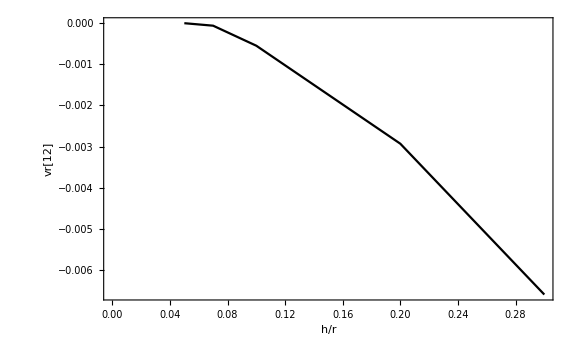

```mathematica
hlist={.05,.07,.1,.2,.3};
λo = 1; λi =10^(-3); ri=1; Γ=0; ro=100; α= 6/(h 10^3) ;
clist = Table[ColorData[1][i],{i,1,Length[hlist]}]
lams={};
plts= {};
plts1={};
mdots={};
vrs={};
For[i=1,i≤ Length[hlist],i++,h=hlist[[i]];Print[h]; sol=NDSolve[ {3 nu[r] λ'[r] + λ[r](3 nu[r](γ-.5)/r - PlanetFlag Func[r]/(Pi Sqrt[r]))== m[r],m'[r]== 0,λ[ri]== λi,λ[ro]== λo},{λ,m},{r,ri,ro}];
AppendTo[mdots,Evaluate[m[ri]/.sol][[1]]];
AppendTo[vrs,Evaluate[m[r]/(-λ[r])/.sol][[1]]];
AppendTo[lams,Evaluate[λ[r]/.sol]];
AppendTo[plts,LogLogPlot[{Evaluate[λ[r]/.sol],αdisk[r,ro]},{r,ri,ro},Frame->True,Axes->False,FrameLabel->{"r","λ"},PlotStyle->{clist[[i]],{Dashed,Gray}}]];
AppendTo[plts1,LogPlot[vrs[[i]]/vrn[r,ro],{r,ri,ro},Frame->True,Axes->False,PlotRange->Full,FrameLabel->{"r","vr/vrn"},PlotStyle->{clist[[i]]}]];]
Show[plts]
ListLogLogPlot[Thread[{hlist,mdots}],Joined->True,Frame->True,Axes->False,FrameLabel->{"h/r","Mdot"},PlotStyle->Black]
Show[Reverse[Reverse[plts1]]]
ListPlot[Thread[{hlist,Table[vrs[[i]]/.r-> 12,{i,1,Length[rilist]}]}],Joined->True,Frame->True,Axes->False,FrameLabel->{"h/r","vr[12]"},PlotStyle->Black]
```

```mathematica
Standard Torque Density
```

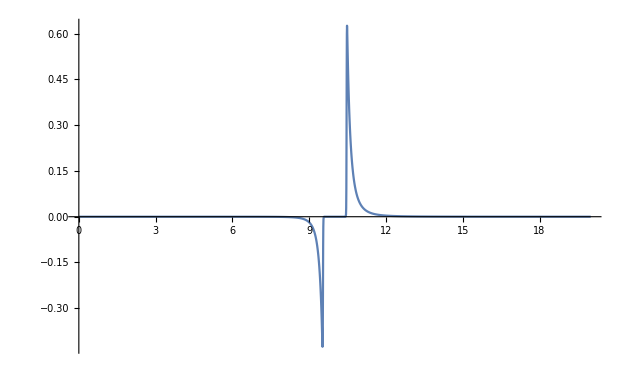

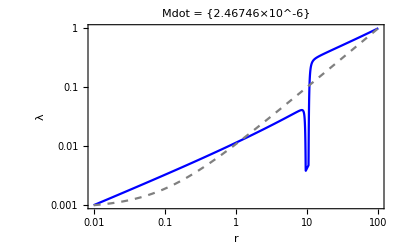

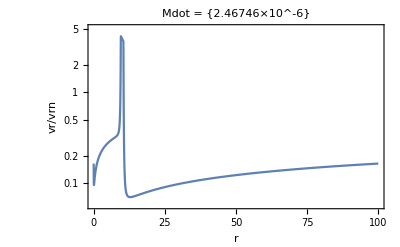

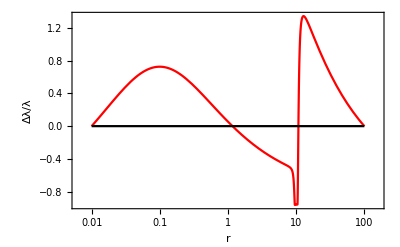

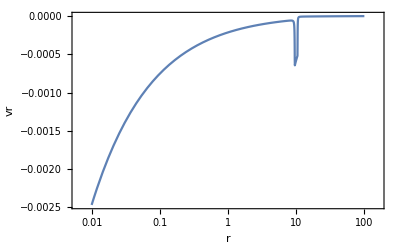

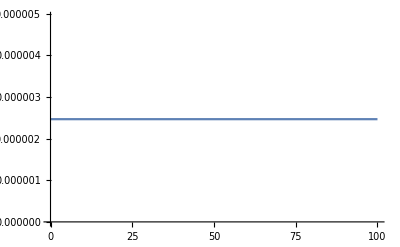

```mathematica
Λf = .9; Λc=2/3; Λw=.01;
λi = .001; λo = 1; ri=.01; ro= 100; h = .1; α = .1;
Plot[Λsmooth[r,Λf,Λc,Λw],{r,ri,a+10},PlotRange->Full]
sol=NDSolve[ {3 nu[r] λ'[r] + λ[r](3 nu[r](γ-.5)/r - PlanetFlag  Λsmooth[r,Λf,Λc,Λw] /(Pi  Sqrt[r])) == m[r],m'[r]== 0,λ[ri]== λi,λ[ro]== λo},{λ,m},{r,ri,ro}];
LogLogPlot[{λ[r]/.sol,αdisk[r,ro]},{r,ri,ro},PlotRange-> {{ri,ro},{λi,λo}},Frame-> True,Axes->False,FrameLabel->{"r","λ"},PlotLabel->  Row@{"Mdot = ", Evaluate[m[ri]/.sol]},PlotStyle->{Blue,{Dashed,Gray}}]
LogPlot[Evaluate[-m[ri]/λ[r]/vrn[r,ro]/.sol],{r,ri,ro},PlotRange-> Full,Frame-> True,Axes->False,FrameLabel->{"r","vr/vrn"},PlotLabel->  Row@{"Mdot = ", Evaluate[m[ri]/.sol]}]
LogLinearPlot[{Evaluate[((λ[r]-αdisk[r,ro])/αdisk[r,ro])/.sol],0},{r,ri,ro},PlotStyle->{Red,Black},PlotRange-> Full,Frame-> True,Axes->False,FrameLabel->{"r","Δλ/λ"}]
LogLinearPlot[Evaluate[-m[r]/λ[r]/.sol],{r,ri,ro},PlotRange-> Full,Frame-> True,Axes->False,FrameLabel->{"r","vr"}]

Plot[m[r]/.sol,{r,ri,ro}]
```

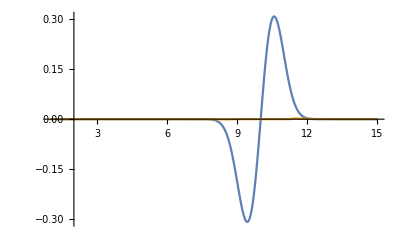

```mathematica
Plot[{Func[r],Λsmooth[r,.2,2,.1]},{r,1,15},PlotRange->Full]
```